```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

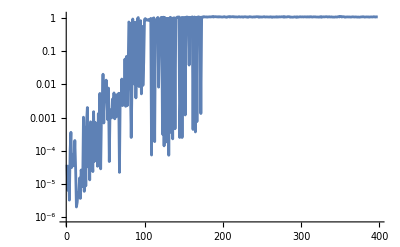

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q1EkG→153.59,Q2EkG→-148.788,Q3EkG→112.843,Q4EkG→116.378,Q5EkG→-27.5081,Q6EkG→-135.531,S1ELkG→1051.01,S2ELkG→-3387.72,S3ELkG→-1847.66,S3ERkG→-766.769,S2ERkG→-2999.86,S1ERkG→971.743,PDrive_mean_x→-3.4075×10^-6,PDrive_mean_y→2.532×10^-7,PDrive_sigma_x→0.000107759,PDrive_sigma_y→0.0000425759,PDrive_mean_xp→0.0000233987,PDrive_mean_yp→8.39×10^-8,PDrive_xCost→0.000107813,PDrive_yCost→0.0000425766,PDrive_totalCost→0.0000751949,PDrive_emitSI90_x→0.00010247,PDrive_emitSI90_y→5.6788×10^-6,PDrive_zLen→0.0000207194,PDrive_zCentroid→991.332,PWitness_mean_x→2.3752×10^-6,PWitness_mean_y→-1.28×10^-8,PWitness_sigma_x→0.0000304531,PWitness_sigma_y→0.0000293496,PWitness_mean_xp→-0.000155238,PWitness_mean_yp→2.047×10^-7,PWitness_xCost→0.0000305456,PWitness_yCost→0.0000293496,PWitness_totalCost→0.0000299476,PWitness_emitSI90_x→0.0000688397,PWitness_emitSI90_y→4.2215×10^-6,PWitness_zLen→0.0000207788,PWitness_zCentroid→991.332,bunchSpacing→0.000208946,transverseCentroidOffset→5.7889×10^-6,maximizeMe→1.12039|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q1EkG : 153.5900133994
Q2EkG : -148.7876856759
Q3EkG : 112.8427631224
Q4EkG : 116.377567229
Q5EkG : -27.5080891886
Q6EkG : -135.5313379509
S1ELkG : 1051.0086088594
S2ELkG : -3387.7189418016
S3ELkG : -1847.6602632478
S3ERkG : -766.7692404155
S2ERkG : -2999.8576018448
S1ERkG : 971.7426479759
PDrive_mean_x : -3.4075e-6
PDrive_mean_y : 2.532e-7
PDrive_sigma_x : 0.0001077594
PDrive_sigma_y : 0.0000425759
PDrive_mean_xp : 0.0000233987
PDrive_mean_yp : 8.39e-8
PDrive_xCost : 0.0001078132
PDrive_yCost : 0.0000425766
PDrive_totalCost : 0.0000751949
PDrive_emitSI90_x : 0.0001024701
PDrive_emitSI90_y : 5.6788e-6
PDrive_zLen : 0.0000207194
PDrive_zCentroid : 991.3316887094
PWitness_mean_x : 2.3752e-6
PWitness_mean_y : -1.28e-8
PWitness_sigma_x : 0.0000304531
PWitness_sigma_y : 0.0000293496
PWitness_mean_xp : -0.0001552375
PWitness_mean_yp : 2.047e-7
PWitness_xCost : 0.0000305456
PWitness_yCost : 0.0000293496
PWitness_totalCost : 0.0000299476
PWitness_emitSI90_x : 0.0000688397
PWitness_emitSI90_y : 4.2215e-6
PWitness_zLen : 0.0000207788
PWitness_zCentroid : 991.331897655
bunchSpacing : 0.0002089456
transverseCentroidOffset : 5.7889e-6
maximizeMe : 1.1203854448

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

5.78881×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv